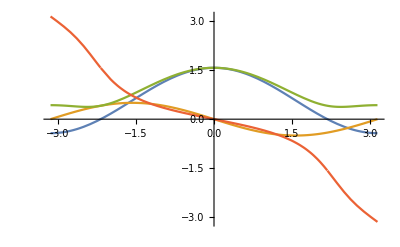

```mathematica
nn=501;
ll=IntegerPart[nn/10];
prec=128;
nData=200;
γ=1/2//N[#,prec]&;
λ=4/7//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
α[θ_]=(a0+(a2+a1) Cos[θ]);
β[θ_]=(a1-a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[α[θ],β[θ]];
Plot[{α[x],β[x],ω[x],ϕ[x]},{x,-π,π}]
```

```mathematica
t=Table[k,{k,-(nn-1)/2,(nn-1)/2}];
μ=2//N[#,prec]&;
βT=RandomReal[{1/1000,1/1100}]//N[#,prec]&;
p[l_]=1/(Exp[βT (ω[((2 π)/nn) l]-μ)]+1);
rand=Table[RandomReal[π],{k,1,(nn-1)/2}];
Data=Table[
mCos=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mCos0=If[RandomReal[]>p[0],-(1/2),1/2];
mSin=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mSin0=If[RandomReal[]>p[0],-(1/2),1/2];
MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] (ϕ[Abs[(2 π)/nn #]]+rand⟦Abs[#]⟧))&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
(*MEspRed=
Table[RotateRight[Take[MPlusBand,ll],j-1],{j,ll}]
+Table[RotateLeft[Take[MMinusAntiBand,ll],j-1],{j,ll}];
Flatten[MEspRed]-Mean[Flatten[MEspRed]],*)
Join[Take[MPlusBand,ll],Take[MMinusAntiBand,ll]],
{ii,nData}];
```

```mathematica
A=(Mean/@Data);
```

```mathematica
DataCentered=Data-(A);
```

```mathematica
Dimensions[A]
```

{2500}

```mathematica
Dimensions[(Mean/Data)]
```

{2500,100}

```mathematica
Dimensions[Data⟦1⟧]
```

{100}